```mathematica
(* Create global definitions and set up workspace for all subsequent work *)
ClearAll["Global`*"];
OpenFigsUsingShell=True;(* If running in batch mode, figures should be opened using shell command *)
If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]];OpenFigsUsingShell=False];
(* If running from the Notebook interface *)
(* If running from shell, must start from inside same directory in which notebook resides *)
```

```mathematica
<<setup_workspace.m;
(* Read in baseline parameters and construct baseline shocks then make discreteApprox figure *)
<<setup_params.m;
<<setup_shocks.m;
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Exporting:discreteApprox

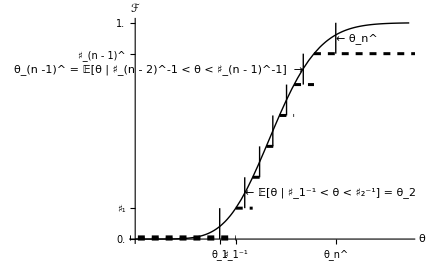

```mathematica
<<discreteApprox!Plot.m;
```

Solve 2period model using brute force (no tricks or approximations) and plot.

Exporting:vTm1Plot

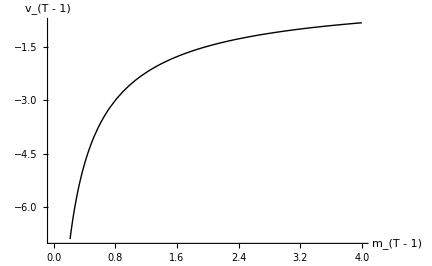

Exporting:cTm1Plot

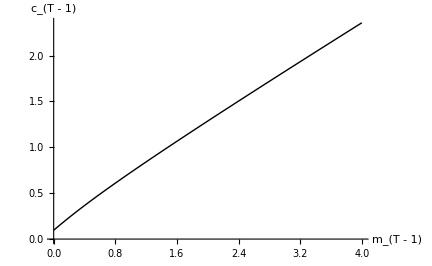

```mathematica
<<2Period!Plot.m;
```

Solve 2period model using linear interpolation.

Exporting:PlotVTm1Simple

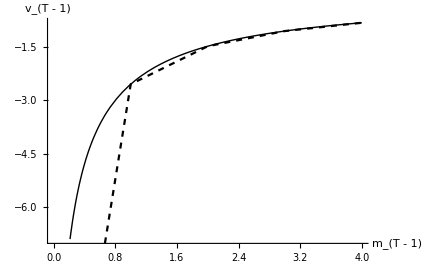

Exporting:PlotcTm1Simple

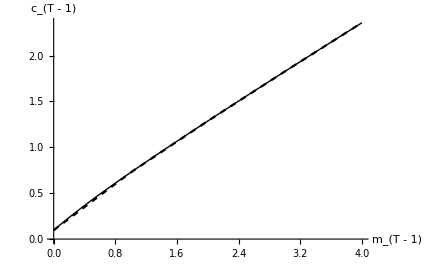

```mathematica
<<2PeriodInt!Plot.m;
```

InterpolatingFunction::dmval: Input value {-0.0663635} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0663574} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0663695} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

Solve 2period model by interpolating expectations.

Exporting:PlotOTm1RawVSInt

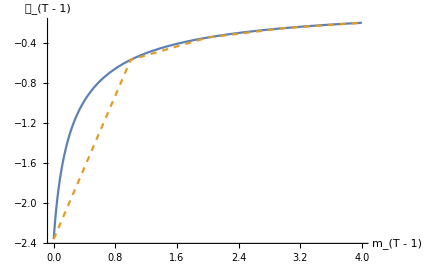

Exporting:PlotCompareVTm1AB

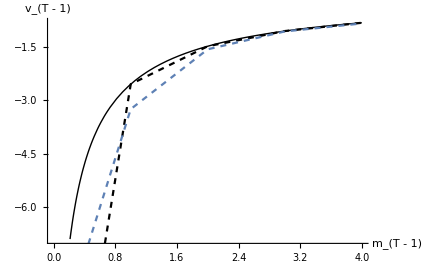

Exporting:PlotComparecTm1AB

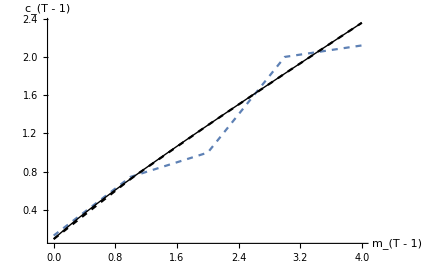

Exporting:PlotuPrimeVSOPrime

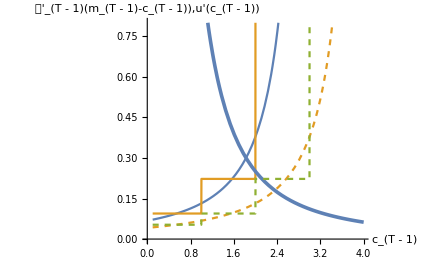

```mathematica
<<2periodIntExp!Plot.m;
```

InterpolatingFunction::dmval: Input value {-0.0663635} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Solve using the FOC, rather than the level of value.

Exporting:PlotGothVRawVSFOC

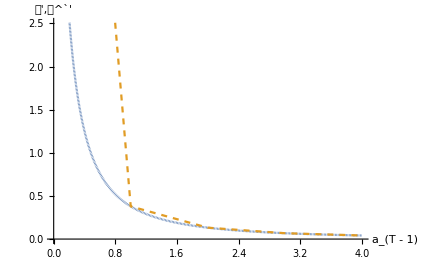

Exporting:PlotcTm1ABC

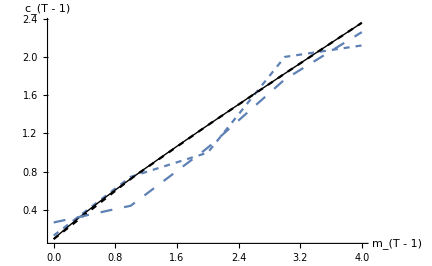

```mathematica
<<2periodIntExpFOC!Plot.m;
```

Solve using the inverse (transformed) versions of the functions.

Exporting:GothVInvVSGothC

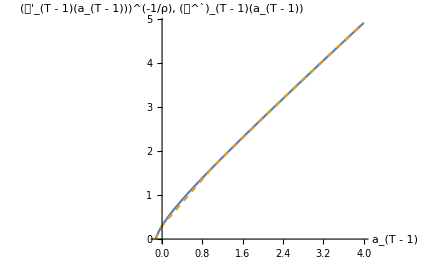

Exporting:GothVVSGothCInv

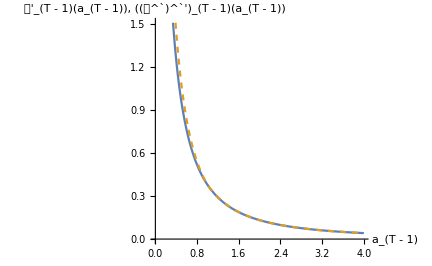

Exporting:PlotComparecTm1AD

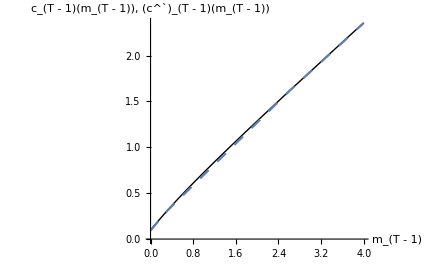

```mathematica
<<2periodIntExpFOCInv!Plot.m;
```

Use a triple-exponential to construct aVec.

Exporting:GothVInvVSGothCEEE

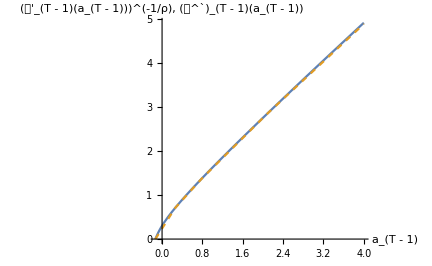

Exporting:GothVVSGothCInvEEE

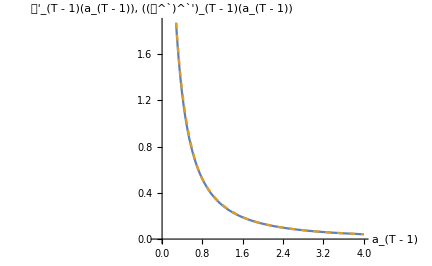

Exporting:PlotComparecTm1ADEEE

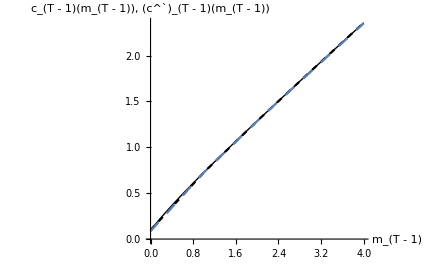

```mathematica
<<2periodIntExpFOCInvEEE!Plot.m;
```

Exporting:ExtrapProblemPlot

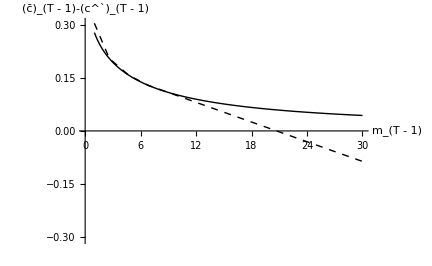

```mathematica
<<ExtrapProblem!Plot.m;
```

Exporting:ExtrapProblemSolvedPlot

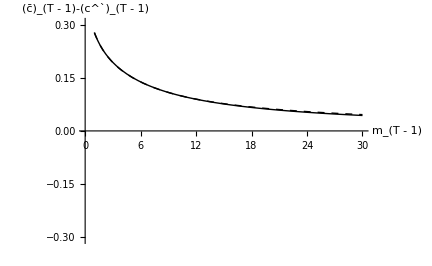

```mathematica
<<ExtrapProblemSolved!Plot.m;
```

Use the 'method of moderation, without tighter upper bound refinement.'

Exporting:IntExpFOCInvPesReaOptGapPlot

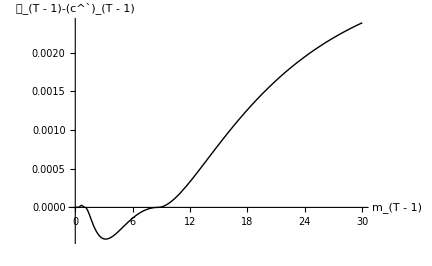

```mathematica
<<2PeriodIntExpFOCInvPesReaOpt!Plot.m;
```

Use the 'method of moderation, with tighter upper bound refinement.'

InterpolatingFunction::dmval: Input value {-10.0812} lies outside the range of data in the interpolating function. Extrapolation will be used.

Exporting:IntExpFOCInvPesReaOptNeedTighterUpBdPlot

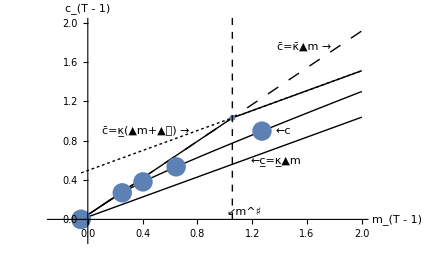

InterpolatingFunction::dmval: Input value {-10.0812} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0489777} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Exporting:IntExpFOCInvPesReaOptNeedTighterUpBdValuePlot

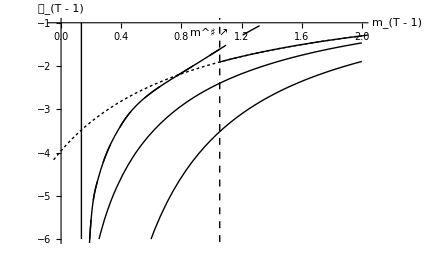

Difference in consumption function before and after tighter upper bound refinement.

Exporting:IntExpFOCInvPesReaOptTighterUpBdGapPlot

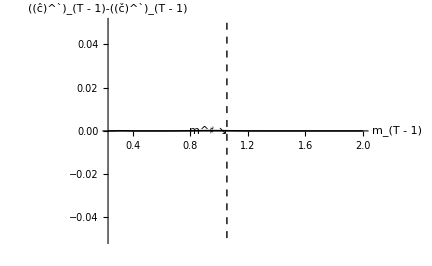

Exporting:IntExpFOCInvPesReaOptTighterUpBdValueGapPlot

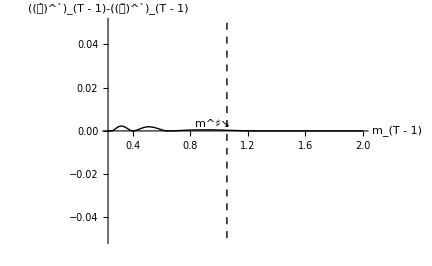

```mathematica
<<2PeriodIntExpFOCInvPesReaOptTighterUpBd!Plot.m;
```

InterpolatingFunction::dmval: Input value {-3.48676} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0184196} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.27874} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Exporting:PlotCFuncsConverge

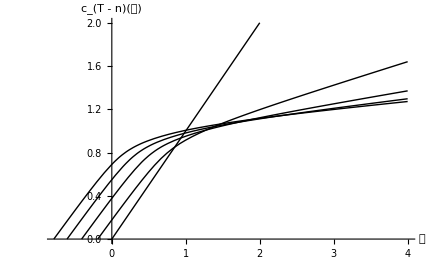

```mathematica
<<multiperiod!Plot.m;
```

Use the 'method of moderation' to solve constrained model.'

InterpolatingFunction::dmval: Input value {-9.4001} lies outside the range of data in the interpolating function. Extrapolation will be used.

Exporting:cVScCon

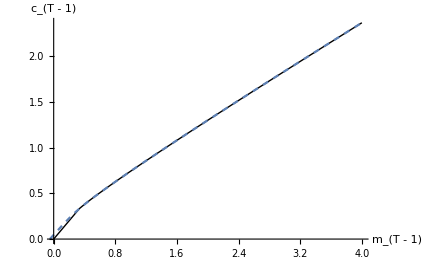

```mathematica
<<2PeriodIntExpFOCInvPesReaOptTighterUpBdCon!Plot.m;
```

Exporting:PlotCFuncsConverge

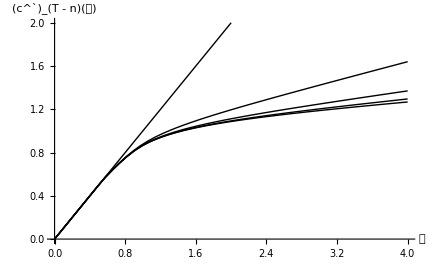

```mathematica
<<multiperiodCon!Plot.m;
```

InterpolatingFunction::dmval: Input value {133.949} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {134.067} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {134.142} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Exporting:PlotctMultContr

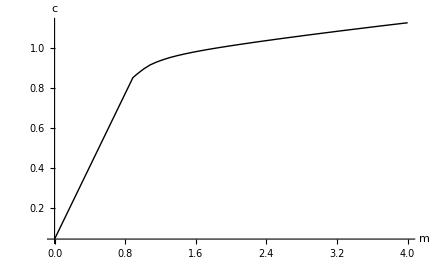

Exporting:PlotRiskySharetOfat

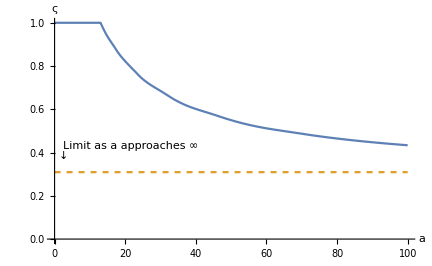

```mathematica
<<multicontrol!Plot.m;
```